```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
ufun=NDSolveValue[{D[u[x,t],t]==0.1* D[u[x,t],{x,2}],
u[0,t]==0,u[1,t]==0,u[x,0]==Sin[π x]},
u,{x,0,1},{t,0,1}];
Plot3D[ufun[x,t],{x,0,1},{t,0,1},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
ufun=NDSolveValue[{D[u[x,t],t]==0.1* D[u[x,t],{x,2}],
u[0,t]==0,u[1,t]==0,u[x,0]==Sin[π x]},
u,{x,0,1},{t,0,1}];
Plot3D[ufun[x,t],{x,0,1},{t,0,1},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

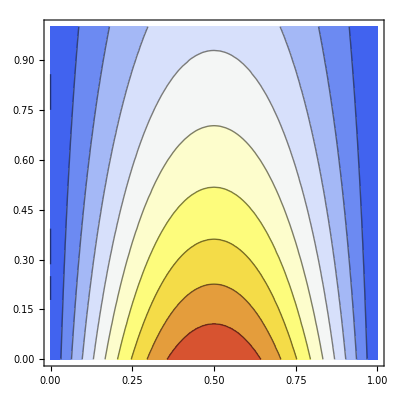

InterpolatingFunction[…]

```mathematica
ContourPlot[ufun[x,t],{x,0,1},{t,0,1},ColorFunction->"Temperature",AspectRatio->Automatic]
```